```mathematica
Needs["DatabaseLink`"]
```

```mathematica
OpenSQLConnection[]
```

$Canceled

```mathematica
conn=Quiet[OpenSQLConnection[JDBC["cc.blynk.clickhouse.ClickHouseDriver","jdbc:clickhouse://localhost:8123"],"Username"->"default"]]
```

SQLConnection[…]

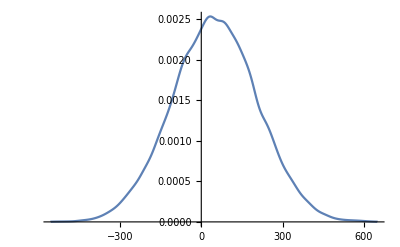

```mathematica
SmoothHistogram[Flatten[SQLExecute[conn, "select `position` from hammy.incremental where time = 50000"]]]
```

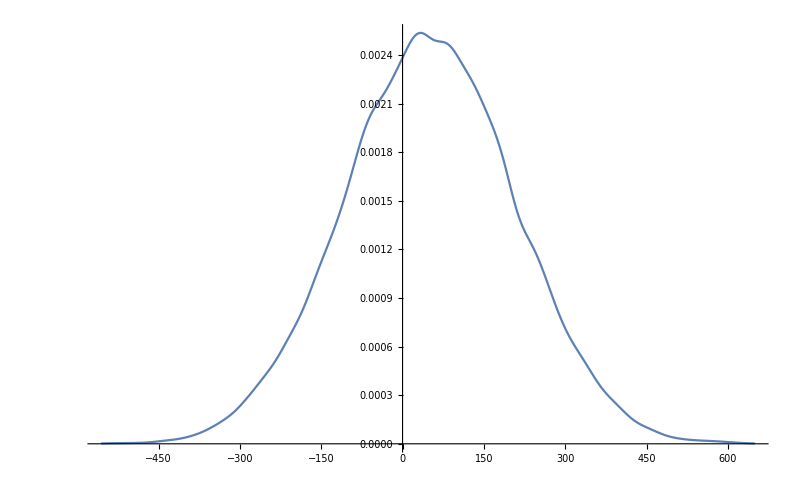

```mathematica
plot=SmoothHistogram[Flatten[SQLExecute[conn,"select `position` from hammy.incremental where time = 50000 "]]]
```

```mathematica
pts1=Join@@Cases[plot,Line[p__]:>p,∞]
```

{{-574.956,0.},{-574.956,0.},{-573.541,1.96888×10^-6},{-572.126,2.10537×10^-6},{-570.711,2.24596×10^-6},{-569.296,2.39027×10^-6},{-567.881,2.53789×10^-6},{-566.465,2.68836×10^-6},{-565.05,2.84116×10^-6},{-563.635,2.99579×10^-6},{-562.22,3.15168×10^-6},{-560.805,3.30827×10^-6},{-559.39,3.46497×10^-6},{-557.975,3.62118×10^-6},{-556.559,3.77634×10^-6},{-555.144,3.92985×10^-6},{-553.729,4.08116×10^-6},{-552.314,4.22976×10^-6},{-550.899,4.37513×10^-6},{-549.484,4.51682×10^-6},{-548.069,4.65445×10^-6},{-546.653,4.78766×10^-6},{-545.238,4.91619×10^-6},{-543.823,5.03986×10^-6},{-542.408,5.15851×10^-6},{-540.993,5.2721×10^-6},{-539.578,5.38067×10^-6},{-538.163,5.48435×10^-6},{-536.747,5.58334×10^-6},{-535.332,5.67795×10^-6},{-533.917,5.76855×10^-6},{-532.502,5.85559×10^-6},{-531.087,5.9396×10^-6},{-529.672,6.02117×10^-6},{-528.257,6.10097×10^-6},{-526.841,6.1797×10^-6},{-525.426,6.25812×10^-6},{-524.011,6.33703×10^-6},{-522.596,6.41724×10^-6},{-521.181,6.49955×10^-6},{-519.766,6.58479×10^-6},{-518.35,6.67379×10^-6},{-516.935,6.76733×10^-6},{-515.52,6.86618×10^-6},{-514.105,6.97108×10^-6},{-512.69,7.0827×10^-6},{-511.275,7.20166×10^-6},{-509.86,7.32854×10^-6},{-508.444,7.46381×10^-6},{-507.029,7.60792×10^-6},{-505.614,7.7612×10^-6},{-504.199,7.92394×10^-6},{-502.784,8.09632×10^-6},{-501.369,8.27848×10^-6},{-499.954,8.47049×10^-6},{-498.538,8.67227×10^-6},{-497.123,8.8838×10^-6},{-495.708,9.10494×10^-6},{-494.293,9.33549×10^-6},{-492.878,9.57524×10^-6},{-491.463,9.82396×10^-6},{-490.048,0.0000100814},{-488.632,0.0000103473},{-487.217,0.0000106213},{-485.802,0.0000109032},{-484.387,0.0000111927},{-482.972,0.0000114896},{-481.557,0.0000117938},{-480.142,0.0000121051},{-478.726,0.0000124234},{-477.311,0.0000127487},{-475.896,0.0000130809},{-474.481,0.0000134203},{-473.066,0.0000137669},{-471.651,0.000014121},{-470.236,0.0000144828},{-468.82,0.0000148528},{-467.405,0.0000152313},{-465.99,0.0000156189},{-464.575,0.0000160161},{-463.16,0.0000164236},{-461.745,0.000016842},{-460.33,0.000017272},{-458.914,0.0000177144},{-457.499,0.0000181699},{-456.084,0.0000186394},{-454.669,0.0000191238},{-453.254,0.0000196239},{-451.839,0.0000201405},{-450.424,0.0000206746},{-449.008,0.0000212271},{-447.593,0.0000217988},{-446.178,0.0000223907},{-444.763,0.0000230035},{-443.348,0.0000236382},{-441.933,0.0000242957},{-440.518,0.0000249767},{-439.102,0.0000256821},{-437.687,0.0000264127},{-436.272,0.0000271693},{-434.857,0.0000279527},{-433.442,0.0000287636},{-432.027,0.0000296028},{-430.611,0.000030471},{-429.196,0.000031369},{-427.781,0.0000322975},{-426.366,0.0000332572},{-424.951,0.0000342489},{-423.536,0.0000352732},{-422.121,0.0000363309},{-420.705,0.0000374228},{-419.29,0.0000385495},{-417.875,0.0000397118},{-416.46,0.0000409105},{-415.045,0.0000421464},{-413.63,0.0000434201},{-412.215,0.0000447325},{-410.799,0.0000460842},{-409.384,0.0000474761},{-407.969,0.000048909},{-406.554,0.0000503834},{-405.139,0.0000519002},{-403.724,0.00005346},{-402.309,0.0000550633},{-400.893,0.0000567108},{-399.478,0.000058403},{-398.063,0.0000601402},{-396.648,0.0000619228},{-395.233,0.0000637509},{-393.818,0.0000656247},{-392.403,0.0000675439},{-390.987,0.0000695084},{-389.572,0.0000715177},{-388.157,0.0000735713},{-386.742,0.0000756683},{-385.327,0.0000778076},{-383.912,0.000079988},{-382.497,0.000082208},{-381.081,0.0000844657},{-379.666,0.0000867591},{-378.251,0.000089086},{-376.836,0.0000914438},{-375.421,0.0000938298},{-374.006,0.000096241},{-372.591,0.0000986739},{-371.175,0.000101125},{-369.76,0.000103591},{-368.345,0.000106068},{-366.93,0.000108552},{-365.515,0.000111039},{-364.1,0.000113525},{-362.685,0.000116005},{-361.269,0.000118476},{-359.854,0.000120933},{-358.439,0.000123373},{-357.024,0.000125792},{-355.609,0.000128186},{-354.194,0.000130552},{-352.779,0.000132888},{-351.363,0.000135189},{-349.948,0.000137455},{-348.533,0.000139684},{-347.118,0.000141874},{-345.703,0.000144025},{-344.288,0.000146137},{-342.872,0.000148211},{-341.457,0.000150247},{-340.042,0.000152248},{-338.627,0.000154216},{-337.212,0.000156154},{-335.797,0.000158066},{-334.382,0.000159957},{-332.966,0.000161833},{-331.551,0.000163697},{-330.136,0.000165558},{-328.721,0.000167421},{-327.306,0.000169295},{-325.891,0.000171186},{-324.476,0.000173104},{-323.06,0.000175055},{-321.645,0.00017705},{-320.23,0.000179095},{-318.815,0.000181201},{-317.4,0.000183376},{-315.985,0.000185627},{-314.57,0.000187965},{-313.154,0.000190395},{-311.739,0.000192927},{-310.324,0.000195567},{-308.909,0.000198321},{-307.494,0.000201195},{-306.079,0.000204196},{-304.664,0.000207326},{-303.248,0.000210589},{-301.833,0.000213988},{-300.418,0.000217526},{-299.003,0.000221201},{-297.588,0.000225015},{-296.173,0.000228967},{-294.758,0.000233053},{-293.342,0.000237271},{-291.927,0.000241616},{-290.512,0.000246085},{-289.097,0.000250671},{-287.682,0.000255366},{-286.267,0.000260165},{-284.852,0.000265059},{-283.436,0.00027004},{-282.021,0.000275098},{-280.606,0.000280224},{-279.191,0.00028541},{-277.776,0.000290644},{-276.361,0.000295918},{-274.946,0.000301222},{-273.53,0.000306548},{-272.115,0.000311886},{-270.7,0.000317228},{-269.285,0.000322566},{-267.87,0.000327895},{-266.455,0.000333209},{-265.04,0.000338501},{-263.624,0.00034377},{-262.209,0.000349013},{-260.794,0.000354228},{-259.379,0.000359415},{-257.964,0.000364576},{-256.549,0.000369714},{-255.133,0.000374834},{-253.718,0.00037994},{-252.303,0.000385041},{-250.888,0.000390143},{-249.473,0.000395257},{-248.058,0.000400394},{-246.643,0.000405565},{-245.227,0.000410782},{-243.812,0.00041606},{-242.397,0.000421413},{-240.982,0.000426854},{-239.567,0.000432399},{-238.152,0.000438063},{-236.737,0.00044386},{-235.321,0.000449807},{-233.906,0.000455916},{-232.491,0.000462202},{-231.076,0.000468678},{-229.661,0.000475356},{-228.246,0.000482247},{-226.831,0.00048936},{-225.415,0.000496704},{-224.,0.000504286},{-222.585,0.000512112},{-221.17,0.000520183},{-219.755,0.000528504},{-218.34,0.000537074},{-216.925,0.000545891},{-215.509,0.000554952},{-214.094,0.000564252},{-212.679,0.000573784},{-211.264,0.000583542},{-209.849,0.000593513},{-208.434,0.000603689},{-207.019,0.000614058},{-205.603,0.000624605},{-204.188,0.000635319},{-202.773,0.000646183},{-201.358,0.000657184},{-199.943,0.000668308},{-198.528,0.000679538},{-197.113,0.000690861},{-195.697,0.000702262},{-194.282,0.000713728},{-192.867,0.000725245},{-191.452,0.000736803},{-190.037,0.000748391},{-188.622,0.000759999},{-187.207,0.000771619},{-185.791,0.000783244},{-184.376,0.00079487},{-182.961,0.000806492},{-181.546,0.00081811},{-180.131,0.000829721},{-178.716,0.000841328},{-177.301,0.000852933},{-175.885,0.00086454},{-174.47,0.000876153},{-173.055,0.000887779},{-171.64,0.000899425},{-170.225,0.000911099},{-168.81,0.000922809},{-167.394,0.000934564},{-165.979,0.000946374},{-164.564,0.000958247},{-163.149,0.000970194},{-161.734,0.000982221},{-160.319,0.000994339},{-158.904,0.00100655},{-157.488,0.00101887},{-156.073,0.0010313},{-154.658,0.00104384},{-153.243,0.0010565},{-151.828,0.00106928},{-150.413,0.00108219},{-148.998,0.00109521},{-147.582,0.00110835},{-146.167,0.00112161},{-144.752,0.00113498},{-143.337,0.00114845},{-141.922,0.00116203},{-140.507,0.0011757},{-139.092,0.00118945},{-137.676,0.00120327},{-136.261,0.00121716},{-134.846,0.00123111},{-133.431,0.00124509},{-132.016,0.00125912},{-130.601,0.00127316},{-129.186,0.00128722},{-127.77,0.00130128},{-126.355,0.00131533},{-124.94,0.00132937},{-123.525,0.00134338},{-122.11,0.00135736},{-120.695,0.00137131},{-119.28,0.00138521},{-117.864,0.00139907},{-116.449,0.00141288},{-115.034,0.00142664},{-113.619,0.00144034},{-112.204,0.00145399},{-110.789,0.00146759},{-109.374,0.00148114},{-107.958,0.00149464},{-106.543,0.0015081},{-105.128,0.00152151},{-103.713,0.00153489},{-102.298,0.00154823},{-100.883,0.00156154},{-99.4675,0.00157482},{-98.0524,0.00158808},{-96.6372,0.00160132},{-95.2221,0.00161453},{-93.8069,0.00162774},{-92.3918,0.00164092},{-90.9767,0.00165409},{-89.5615,0.00166724},{-88.1464,0.00168037},{-86.7312,0.00169348},{-85.3161,0.00170657},{-83.9009,0.00171962},{-82.4858,0.00173264},{-81.0706,0.00174562},{-79.6555,0.00175856},{-78.2403,0.00177143},{-76.8252,0.00178425},{-75.4101,0.001797},{-73.9949,0.00180967},{-72.5798,0.00182226},{-71.1646,0.00183475},{-69.7495,0.00184716},{-68.3343,0.00185946},{-66.9192,0.00187166},{-65.504,0.00188375},{-64.0889,0.00189574},{-62.6737,0.00190762},{-61.2586,0.0019194},{-59.8435,0.00193108},{-58.4283,0.00194266},{-57.0132,0.00195416},{-55.598,0.00196558},{-54.1829,0.00197694},{-52.7677,0.00198825},{-51.3526,0.00199952},{-49.9374,0.00201077},{-48.5223,0.00202202},{-47.1072,0.00203328},{-45.692,0.00204458},{-44.2769,0.00205594},{-42.8617,0.00206737},{-41.4466,0.00207889},{-40.0314,0.00209052},{-38.6163,0.00210228},{-37.2011,0.00211419},{-35.786,0.00212626},{-34.3708,0.0021385},{-32.9557,0.00215093},{-31.5406,0.00216355},{-30.1254,0.00217636},{-28.7103,0.00218938},{-27.2951,0.00220259},{-25.88,0.002216},{-24.4648,0.0022296},{-23.0497,0.00224337},{-21.6345,0.0022573},{-20.2194,0.00227138},{-18.8042,0.00228557},{-17.3891,0.00229986},{-15.974,0.00231422},{-14.5588,0.00232861},{-13.1437,0.00234301},{-11.7285,0.00235738},{-10.3134,0.00237167},{-8.89823,0.00238585},{-7.48309,0.00239989},{-6.06794,0.00241373},{-4.6528,0.00242734},{-3.23765,0.00244067},{-1.82251,0.00245368},{-0.407362,0.00246634},{1.00778,0.00247861},{2.42293,0.00249044},{3.83807,0.0025018},{5.25322,0.00251267},{6.66836,0.002523},{8.08351,0.00253279},{9.49865,0.00254199},{10.9138,0.0025506},{12.3289,0.00255861},{13.7441,0.00256599},{15.1592,0.00257275},{16.5744,0.00257888},{17.9895,0.00258439},{19.4047,0.00258928},{20.8198,0.00259356},{22.235,0.00259725},{23.6501,0.00260037},{25.0653,0.00260294},{26.4804,0.00260498},{27.8955,0.00260652},{29.3107,0.00260759},{30.7258,0.00260823},{32.141,0.00260847},{33.5561,0.00260834},{34.9713,0.00260788},{36.3864,0.00260712},{37.8016,0.00260611},{39.2167,0.00260488},{40.6318,0.00260346},{42.047,0.00260189},{43.4621,0.00260019},{44.8773,0.00259839},{46.2924,0.00259653},{47.7076,0.00259461},{49.1227,0.00259267},{50.5379,0.00259072},{51.953,0.00258878},{53.3682,0.00258684},{54.7833,0.00258492},{56.1984,0.00258303},{57.6136,0.00258114},{59.0287,0.00257928},{60.4439,0.00257741},{61.859,0.00257554},{63.2742,0.00257365},{64.6893,0.00257172},{66.1045,0.00256973},{67.5196,0.00256766},{68.9347,0.00256549},{70.3499,0.00256319},{71.765,0.00256075},{73.1802,0.00255812},{74.5953,0.00255529},{76.0105,0.00255223},{77.4256,0.00254892},{78.8408,0.00254533},{80.2559,0.00254145},{81.6711,0.00253723},{83.0862,0.00253268},{84.5013,0.00252777},{85.9165,0.00252249},{87.3316,0.00251682},{88.7468,0.00251075},{90.1619,0.00250427},{91.5771,0.00249738},{92.9922,0.00249008},{94.4074,0.00248236},{95.8225,0.00247423},{97.2377,0.00246569},{98.6528,0.00245675},{100.068,0.00244742},{101.483,0.00243771},{102.898,0.00242763},{104.313,0.00241719},{105.729,0.00240643},{107.144,0.00239534},{108.559,0.00238395},{109.974,0.00237229},{111.389,0.00236037},{112.804,0.00234822},{114.219,0.00233585},{115.635,0.0023233},{117.05,0.00231058},{118.465,0.00229772},{119.88,0.00228474},{121.295,0.00227167},{122.71,0.00225852},{124.125,0.00224532},{125.541,0.00223209},{126.956,0.00221885},{128.371,0.00220562},{129.786,0.00219241},{131.201,0.00217924},{132.616,0.00216614},{134.031,0.0021531},{135.447,0.00214015},{136.862,0.00212729},{138.277,0.00211454},{139.692,0.0021019},{141.107,0.00208938},{142.522,0.00207698},{143.937,0.0020647},{145.353,0.00205255},{146.768,0.00204052},{148.183,0.00202862},{149.598,0.00201683},{151.013,0.00200515},{152.428,0.00199358},{153.843,0.00198211},{155.259,0.00197072},{156.674,0.00195942},{158.089,0.00194818},{159.504,0.001937},{160.919,0.00192586},{162.334,0.00191476},{163.749,0.00190368},{165.165,0.00189261},{166.58,0.00188153},{167.995,0.00187045},{169.41,0.00185933},{170.825,0.00184818},{172.24,0.00183698},{173.655,0.00182573},{175.071,0.00181442},{176.486,0.00180304},{177.901,0.00179158},{179.316,0.00178004},{180.731,0.00176841},{182.146,0.0017567},{183.562,0.00174489},{184.977,0.001733},{186.392,0.00172101},{187.807,0.00170892},{189.222,0.00169675},{190.637,0.00168448},{192.052,0.00167212},{193.468,0.00165968},{194.883,0.00164714},{196.298,0.00163453},{197.713,0.00162182},{199.128,0.00160904},{200.543,0.00159618},{201.958,0.00158324},{203.374,0.00157022},{204.789,0.00155712},{206.204,0.00154395},{207.619,0.0015307},{209.034,0.00151737},{210.449,0.00150397},{211.864,0.00149048},{213.28,0.00147692},{214.695,0.00146327},{216.11,0.00144955},{217.525,0.00143574},{218.94,0.00142185},{220.355,0.00140787},{221.77,0.00139381},{223.186,0.00137967},{224.601,0.00136545},{226.016,0.00135115},{227.431,0.00133678},{228.846,0.00132233},{230.261,0.00130782},{231.676,0.00129325},{233.092,0.00127863},{234.507,0.00126397},{235.922,0.00124927},{237.337,0.00123455},{238.752,0.00121982},{240.167,0.00120509},{241.582,0.00119037},{242.998,0.00117568},{244.413,0.00116104},{245.828,0.00114644},{247.243,0.00113193},{248.658,0.0011175},{250.073,0.00110317},{251.488,0.00108897},{252.904,0.00107489},{254.319,0.00106097},{255.734,0.00104722},{257.149,0.00103364},{258.564,0.00102025},{259.979,0.00100706},{261.394,0.000994093},{262.81,0.000981347},{264.225,0.000968833},{265.64,0.000956559},{267.055,0.000944531},{268.47,0.000932752},{269.885,0.000921227},{271.301,0.000909955},{272.716,0.000898937},{274.131,0.000888171},{275.546,0.000877653},{276.961,0.000867379},{278.376,0.000857342},{279.791,0.000847534},{281.207,0.000837947},{282.622,0.00082857},{284.037,0.000819391},{285.452,0.000810397},{286.867,0.000801577},{288.282,0.000792915},{289.697,0.000784396},{291.113,0.000776006},{292.528,0.000767729},{293.943,0.000759549},{295.358,0.00075145},{296.773,0.000743417},{298.188,0.000735434},{299.603,0.000727488},{301.019,0.000719563},{302.434,0.000711647},{303.849,0.000703727},{305.264,0.000695791},{306.679,0.000687831},{308.094,0.000679838},{309.509,0.000671803},{310.925,0.000663721},{312.34,0.000655588},{313.755,0.000647402},{315.17,0.00063916},{316.585,0.000630863},{318.,0.000622514},{319.415,0.000614116},{320.831,0.000605674},{322.246,0.000597193},{323.661,0.000588682},{325.076,0.000580149},{326.491,0.000571603},{327.906,0.000563056},{329.321,0.000554517},{330.737,0.000545999},{332.152,0.000537513},{333.567,0.000529071},{334.982,0.000520685},{336.397,0.000512367},{337.812,0.000504127},{339.227,0.000495976},{340.643,0.000487924},{342.058,0.00047998},{343.473,0.000472152},{344.888,0.000464446},{346.303,0.000456868},{347.718,0.000449422},{349.133,0.000442111},{350.549,0.000434937},{351.964,0.0004279},{353.379,0.000420999},{354.794,0.000414231},{356.209,0.000407594},{357.624,0.000401082},{359.04,0.000394689},{360.455,0.00038841},{361.87,0.000382237},{363.285,0.000376161},{364.7,0.000370174},{366.115,0.000364268},{367.53,0.000358432},{368.946,0.000352659},{370.361,0.000346939},{371.776,0.000341262},{373.191,0.000335621},{374.606,0.000330009},{376.021,0.000324416},{377.436,0.000318838},{378.852,0.000313269},{380.267,0.000307704},{381.682,0.000302139},{383.097,0.000296572},{384.512,0.000291001},{385.927,0.000285426},{387.342,0.000279847},{388.758,0.000274266},{390.173,0.000268685},{391.588,0.000263109},{393.003,0.000257542},{394.418,0.000251989},{395.833,0.000246457},{397.248,0.000240951},{398.664,0.00023548},{400.079,0.000230052},{401.494,0.000224673},{402.909,0.000219354},{404.324,0.000214101},{405.739,0.000208923},{407.154,0.000203829},{408.57,0.000198826},{409.985,0.000193922},{411.4,0.000189124},{412.815,0.000184438},{414.23,0.000179871},{415.645,0.000175427},{417.06,0.000171112},{418.476,0.000166928},{419.891,0.000162879},{421.306,0.000158966},{422.721,0.000155191},{424.136,0.000151554},{425.551,0.000148053},{426.966,0.000144688},{428.382,0.000141455},{429.797,0.000138353},{431.212,0.000135376},{432.627,0.00013252},{434.042,0.000129779},{435.457,0.000127149},{436.872,0.000124623},{438.288,0.000122193},{439.703,0.000119854},{441.118,0.000117598},{442.533,0.000115418},{443.948,0.000113307},{445.363,0.000111257},{446.779,0.000109261},{448.194,0.000107313},{449.609,0.000105406},{451.024,0.000103534},{452.439,0.000101691},{453.854,0.0000998715},{455.269,0.0000980712},{456.685,0.0000962858},{458.1,0.0000945116},{459.515,0.0000927456},{460.93,0.0000909854},{462.345,0.0000892291},{463.76,0.0000874756},{465.175,0.0000857242},{466.591,0.0000839749},{468.006,0.0000822282},{469.421,0.000080485},{470.836,0.0000787468},{472.251,0.0000770154},{473.666,0.0000752931},{475.081,0.0000735822},{476.497,0.0000718856},{477.912,0.0000702063},{479.327,0.0000685471},{480.742,0.0000669114},{482.157,0.0000653023},{483.572,0.000063723},{484.987,0.0000621765},{486.403,0.0000606659},{487.818,0.0000591939},{489.233,0.0000577631},{490.648,0.000056376},{492.063,0.0000550345},{493.478,0.0000537406},{494.893,0.0000524958},{496.309,0.0000513013},{497.724,0.000050158},{499.139,0.0000490663},{500.554,0.0000480267},{501.969,0.0000470389},{503.384,0.0000461026},{504.799,0.0000452169},{506.215,0.0000443809},{507.63,0.0000435932},{509.045,0.0000428523},{510.46,0.0000421562},{511.875,0.000041503},{513.29,0.0000408905},{514.705,0.0000403162},{516.121,0.0000397775},{517.536,0.0000392717},{518.951,0.000038796},{520.366,0.0000383476},{521.781,0.0000379235},{523.196,0.0000375208},{524.611,0.0000371364},{526.027,0.0000367675},{527.442,0.0000364112},{528.857,0.0000360647},{530.272,0.0000357253},{531.687,0.0000353903},{533.102,0.0000350573},{534.518,0.0000347239},{535.933,0.000034388},{537.348,0.0000340476},{538.763,0.000033701},{540.178,0.0000333463},{541.593,0.0000329824},{543.008,0.000032608},{544.424,0.0000322221},{545.839,0.0000318239},{547.254,0.000031413},{548.669,0.000030989},{550.084,0.0000305518},{551.499,0.0000301014},{552.914,0.0000296382},{554.33,0.0000291625},{555.745,0.000028675},{557.16,0.0000281765},{558.575,0.0000276678},{559.99,0.0000271501},{561.405,0.0000266243},{562.82,0.0000260918},{564.236,0.0000255539},{565.651,0.0000250117},{567.066,0.0000244668},{568.481,0.0000239204},{569.896,0.000023374},{571.311,0.000022829},{572.726,0.0000222865},{574.142,0.000021748},{575.557,0.0000212146},{576.972,0.0000206875},{578.387,0.0000201677},{579.802,0.0000196563},{581.217,0.000019154},{582.632,0.0000186617},{584.048,0.0000181801},{585.463,0.0000177097},{586.878,0.0000172509},{588.293,0.0000168043},{589.708,0.0000163698},{591.123,0.0000159479},{592.538,0.0000155385},{593.954,0.0000151415},{595.369,0.0000147569},{596.784,0.0000143844},{598.199,0.0000140238},{599.614,0.0000136746},{601.029,0.0000133365},{602.444,0.0000130089},{603.86,0.0000126914},{605.275,0.0000123834},{606.69,0.0000120843},{608.105,0.0000117934},{609.52,0.0000115101},{610.935,0.0000112337},{612.35,0.0000109637},{613.766,0.0000106993},{615.181,0.0000104399},{616.596,0.0000101849},{618.011,9.93359×10^-6},{619.426,9.68552×10^-6},{620.841,9.4401×10^-6},{622.257,9.19683×10^-6},{623.672,8.95527×10^-6},{625.087,8.71501×10^-6},{626.502,8.47569×10^-6},{627.917,8.23701×10^-6},{629.332,7.99874×10^-6},{630.747,7.7607×10^-6},{632.163,7.52275×10^-6},{633.578,7.28482×10^-6},{634.993,7.04692×10^-6},{636.408,6.80908×10^-6},{637.823,6.5714×10^-6},{639.238,6.33405×10^-6},{640.653,6.09723×10^-6},{642.069,5.86118×10^-6},{643.484,5.62618×10^-6},{644.899,5.39255×10^-6},{646.314,5.16065×10^-6},{647.729,4.93084×10^-6},{649.144,4.70353×10^-6},{650.559,4.47911×10^-6},{651.975,4.25799×10^-6},{653.39,4.0406×10^-6},{654.805,3.82733×10^-6},{656.22,3.61858×10^-6},{657.635,3.41474×10^-6},{659.05,3.21615×10^-6},{660.465,3.02316×10^-6},{661.881,2.83609×10^-6},{663.296,2.65518×10^-6},{664.711,2.48072×10^-6},{666.126,2.3129×10^-6},{667.541,2.15189×10^-6},{668.956,1.99782×10^-6},{670.371,0.},{670.371,0.}}